```mathematica
ClearAll["Global'*"];
Needs["PlotLegends`"](* PlotLegends is now obsolete*) 
Evaluate[{FileNameSetter[Dynamic[datafilename1]],Dynamic[datafilename1]}] 
If[FileExistsQ[datafilename1],Print["File exists "datafilename1],Print["This File does not exist"];Quit[]];
 data1=Import[datafilename1];

memoryTem=0;
mtxw=320; mtxh=240; sw=4; sh=3; 
redw=Round[mtxw/sw]; redh=Round[mtxh/sh];
Temperaturethreshold=.3;  showmesh=False;TechError=0.05;
FilterForErrorMagnitude1=1;

ImageSizeLocal=450;
colorsGoody={RGBColor[0.05374,0,0.333],RGBColor[0.0979,0,0.467],RGBColor[0,0,1],RGBColor[0.2,1,0.96],RGBColor[0,0.93,0.07519],RGBColor[1,1,0],RGBColor[1,0,0],Darker[RGBColor[1,0,0],.4]};

For[i=1,i≤mtxw,i++,{
For[j=1,j≤Round[mtxh/2],j++,{
memoryTem=data1[[(i-1)*mtxh+j,3]];
data1[[(i-1)*mtxh+j,3]]=data1[[(i-1)*mtxh+(mtxh+1-j),3]];
data1[[(i-1)*mtxh+(mtxh+1-j),3]]=memoryTem;
}]
}]
Print["CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}"]
ListDensityPlot[data1,PlotRange->All,ColorFunction->(*colorsGoody*)GrayLevel,Mesh->showmesh,Mesh->{redw-1,redh-1},ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Automatic,ColorFunctionScaling->True,InterpolationOrder->0] 

Mask43=ArrayReshape[Transpose@ArrayReshape[ArrayReshape[Transpose@ArrayReshape[Table[i,{i,mtxw*mtxh}],{mtxw,mtxh}],{redw,mtxh,sw}],{mtxh,redw,sw}],{redw,redh,sw*sh}];

If[Mask43[[redw,redh,sw*sh]]==mtxw*mtxh,Print["CheckPoint#2  - excellent"],Print["CheckPoint#2 - failed!"]]

data2=data1; Clear[data1];
arrenged=Array[{#/#}&,{redw,redh,3}];
For[i=1,i<=Length[arrenged],i++,{
For[j=1,j<=Length[arrenged[[i]]],j++,{
arrenged[[i,j,1]]=(i-0.5)*sw;
arrenged[[i,j,2]]=sh*(j-0.5);

arrenged[[i,j,3]]=Sum[data2[[Mask43[[i,j,a]],3]],{a,sw*sh}]*(1/(sw*sh));
noiseF[x_,av_]:=x-av;
For[a:=1,a≤(sw*sh),a++,{data2[[Mask43[[i,j,a]],3]]=(1/TechError)*noiseF[data2[[Mask43[[i,j,a]],3]],arrenged[[i,j,3]]];
If[Abs@data2[[Mask43[[i,j,a]],3]]>FilterForErrorMagnitude1,data2[[Mask43[[i,j,a]],3]]=0];
}]

  }]

}]

Clear[arrenged,Mask43];
(*For[i=1,i<=Length[data2],i++,If[Abs[data2[[i,3]]]>Temperaturethreshold,data2[[i,3]]=0]]
For[i=1,i<=Length[data2],i++,If[Abs[data2[[i,3]]]>0.1,data2[[i,3]]=Temperaturethreshold]]*)

ListDensityPlot[data2,PlotRange->All,ColorFunction->(*colorsGoody*)GrayLevel,Mesh->showmesh,Mesh->{redw-1,redh-1},ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Automatic,ColorFunctionScaling->True,InterpolationOrder->0]
(*ListPointPlot3D[data1,ColorFunction->Function[{x,y,z},Hue[-z]]]*)

Clear[data2];
```

{,}

C:\A\Notes\PRG\W\gjIR000110.dat File exists

CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}

-Graphics-

CheckPoint#2  - excellent

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
img=;
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];

data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```

```mathematica
img1=;
img2=;
(*preprocess images*)
images={DeleteSmallComponents@Binarize[img1,.2],DeleteSmallComponents@Binarize[img2,.2]};
(*find matching points*)
matches=ImageCorrespondingPoints[images[[1]],images[[2]],"Transformation"->"Translation"];
(*Show points on images*)
MapThread[Show[#1,Graphics[{Cyan,MapIndexed[Inset[#2[[1]],#1]&,#2]}]]&,{images,matches}]
images={DeleteSmallComponents@Binarize[FillingTransform@img1,.2],DeleteSmallComponents@Binarize[FillingTransform@img2,.2]};
matches=ImageCorrespondingPoints[images[[1]],images[[2]],"Transformation"->"Similarity"]
Show[ImageAssemble[images],Graphics[{Red,PointSize[.02],MapThread[If[#2===Missing[],{Cyan,Point[#1]},Arrow[{#1,#2+{ImageDimensions[img1][[1]],0}}]]&,matches]}]]
{i1,i2}=Erosion[DeleteSmallComponents[ChanVeseBinarize[#,TargetColor->Gray]],10]&/@{img1,img2}
c1=1/.ComponentMeasurements[i1,"MinimalBoundingBox"];
c2=1/.ComponentMeasurements[i2,"MinimalBoundingBox"];
Show[ImageCompose[img1,{img2,.5}],Graphics[{Opacity[0.5],White,Polygon[c1],Polygon[c2],Green,Text[#,#]&/@c1,Text[#,#]&/@c2}]]
```

IR110 graylevel

IR111 graylevel

IR112 graylevel

-Graphics-

```mathematica
img1=-Graphics-;
img2=-Graphics-;
img3=-Graphics-;
Row[ImageSubtract[img1,img2],ImageSubtract[img2,img3],ImageSubtract[img1,img3]]
```

Row[-Graphics-,-Graphics-,-Graphics-]

```mathematica
img1x=-Graphics-;
img2x=-Graphics-;
img3x=-Graphics-;
```

IR110 frac dimention

{-Graphics-,-Graphics-}

11.0025+1.7814 x

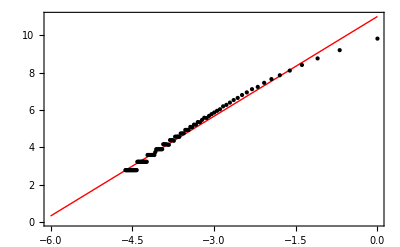

```mathematica
img=-Graphics-;
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];

data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```

IR111 	frac dimention ONLY Grass

{-Graphics-,-Graphics-}

10.7158+1.78739 x

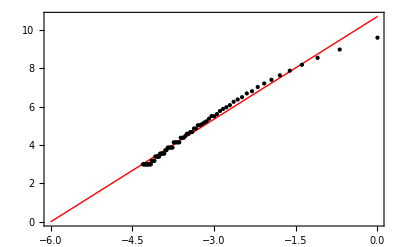

```mathematica
img=-Graphics-;
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];

data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```

IR111 frac dimention

{-Graphics-,-Graphics-}

10.8994+1.76333 x

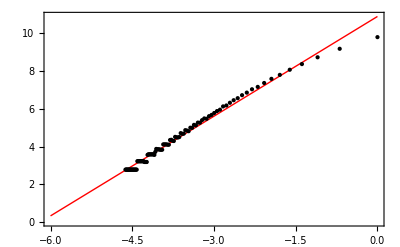

```mathematica
img=-Graphics-;
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];

data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```

IR111  frac dimention only GRASS

{-Graphics-,-Graphics-}

10.6942+1.79667 x

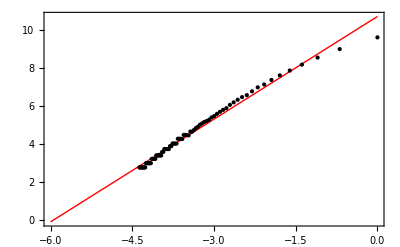

```mathematica
img=-Graphics-;
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];

data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```

IR112 frac dimention

{-Graphics-,-Graphics-}

11.12+1.81232 x

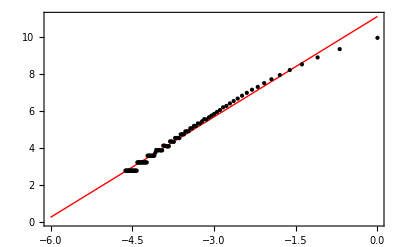

```mathematica
img=-Graphics-;
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];

data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```

IR112 frac dimention ONLY GRASS

{-Graphics-,-Graphics-}

10.8451+1.83598 x

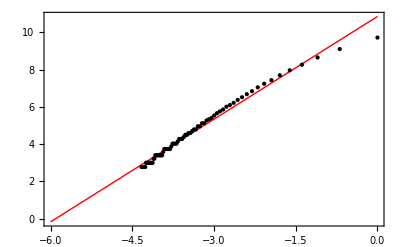

```mathematica
img=-Graphics-;
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];

data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```